# Diffusion-Limited Symphony

The Diffusion-Limited Symphony forges a link between visual art and music, bringing the past into the present through creative expression.  Through diffusion-limited aggregation, this symphony generates organic forms from a few simple rules and translates the image into musical sounds that enliven the harmonies of distant memories.

June 30, 2018—Jiaying Xu

## I. From Something to Nothing, from Nothing to Something

Surrounded by highly talented and astute scientists, I was apprehended by my profound ignorance of the natural world, and was awed at the powerful insights from science about humanity. Trying ironically hard to add a “science-y” touch to my thoughts, I buried myself in introductory books on math, biology and computer science for several sleepless nights, redrafting my computational essay prompt over and over again. I ultimately settled down on the complex idea of applying social network theory to predict the probability of a newly introduced mutant generating a lineage that takes over the whole population. I explained my ideas to my mentor with the graphed structure of population that I was going to analyze, thinking somewhat self-satisfactorily that this essay would perfectly serve as a building block for my final project.

inertia holds me

```mathematica
randomStep[point_]:=point+RandomChoice[{{1,0},{-1,0},{0,1},{0,-1}}]
```

from where to start is unclear

```mathematica
point={0,0};
```

thus I meander

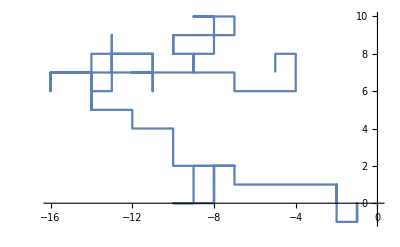

```mathematica
ListLinePlot@Table[point=randomStep@point,100]
```

"Let's forget about this essay for now and start with something simple," my mentor put away my computer and winkled at me. "How about creating a news map that compares news sources horizontally and vertically to generate more accurate information?" I replied. "Still too complicated," he said. Just as fast as each new convoluted thought rushed in my mind to fill any void, my mentor wittily negated all of them and pushed me to think further—in a simpler manner.

thoughts spring into mind

```mathematica
snowflake={{0,0}};
```

too many others to see

```mathematica
walkers=RandomInteger[{-20,20},{250,2}];
```

what can become here

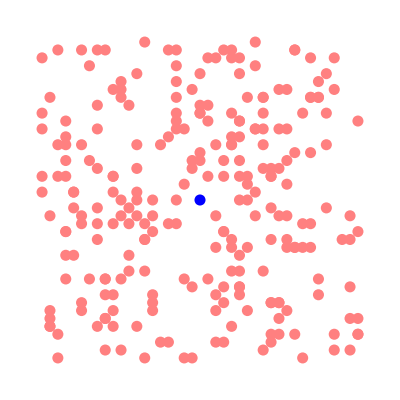

```mathematica
Graphics[{Blue,Disk[#, 0.7]&/@snowflake,Pink,Disk[#,0.7]&/@walkers}]
```

This process of puzzlement and discovery  brought about animated conversation, effectively removing layers and layers of bookish concepts that deterred me from sensing the world as it is. All of a sudden, words such as "nature," "flower," "wind," and "water" from my mentor created a ripple effect in my mind that surprisingly built associations between the growth pattern of a snowflake with music passages from a symphony.

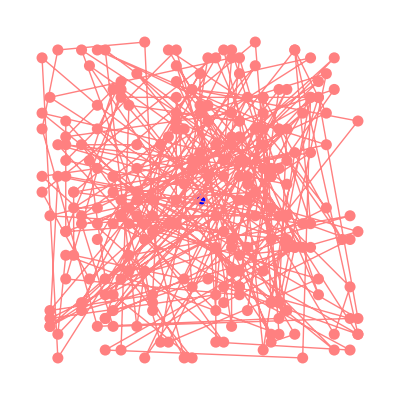

```mathematica
Graphics[{Pink,Disk[#,0.7]&/@walkers,Blue,Disk[#, 0.7]&/@snowflake,Pink,Line@walkers}]
```

To turn this idea into reality, I took my mentor’s advice on self-studying the diffusion-limited aggregation and audio processing with Mathematica. The more I played around with relevant codes, the more I realized the power of simple ideas in generating sophisticated knowledge, as well as that of informal discussion in bringing about fresh insights.

```mathematica
AudioPlay@AudioJoin@RandomSample@AudioPartition[SpeechSynthesize["I am beginning to see the world around me, but my thoughts are still too thick"],.5];
```

## II. From Others to Self, from Self to Others

A chemist would typically explain the formation of a snowflake as follows:

"Ultimately, it is the temperature at which a crystal forms—and to a lesser extent the humidity of the air—that determines the basic shape of the ice crystal. Thus, we see long needle-like crystals at 23 degrees F and very flat plate-like crystals at 5 degrees F.  The intricate shape of a single arm of the snowflake is determined by the atmospheric conditions experienced by entire ice crystal as it falls. A crystal might begin to grow arms in one manner, and then minutes or even seconds later, slight changes in the surrounding temperature or humidity causes the crystal to grow in another way. Although the six-sided shape is always maintained, the ice crystal (and its six arms) may branch off in new directions."

```mathematica
Entity["Mineral","Ice"]["Image"]
```

-Graphics-

Rather than relying on the highly complex rules for growth in the explanation, this diffusion-limited model follows extremely simple rules to achieve similar results with astounding diversity and visual effects. While not fully capturing all factors, such as humidity and temperature, that influence the formation of a snowflake in the real world, this model embodies nevertheless the fundamental principles underlying the growth of a natural object.

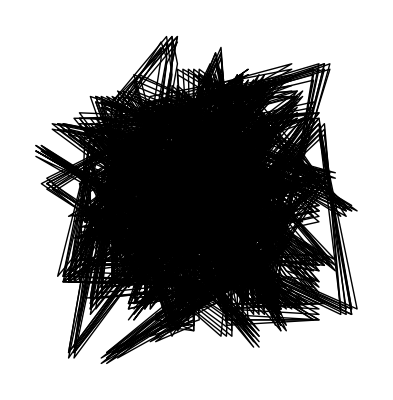

```mathematica
Graphics[Line/@Table[walkers=randomStep/@walkers,10]]
```

## III. From Simplicity to Complexity, from Complexity to Simplicity

This diffusion-limited model beautifully illustrates that an original seed when combined with even a few simple rules can result in apparent randomness. This tumultuous situation is reinforced by the intensifying noise in the background. Following the question in the second section of this essay, I am wondering if it is possible that all randomness results from the application of a minimal number of uncomplicated rules? If so, would keeping the underlying rules and leaving out superfluous factors in real world circumstances (i.e. humidity) justify in turn the power of computational language in approximating the real world? Since for two snowflakes to be exactly identical, identical conditions in nature are required, which is basically impossible, thus the futility of involving those detailed factors into the model considering the random results.

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50]]
```

-Graphics-

Similarly, a music note can be simply depicted as vibrations of mechanical systems measured in hertz (HZ). As is well-known, these fixed frequencies are mathematically related to each other, and can be easily transcribed into computational language. Considering the interconnectedness among various things in this world, this coding experience prompted me to think further about whether all natural phenomena, or even human feelings and behaviors, are explainable by strikingly simple underlying rules.

```mathematica
EmitSound[MapIndexed[SoundNote[#1,RandomReal[],SoundVolume->(First@#2+RandomReal[])/20]&,CellularAutomaton[30,{{1},0},20]]]
```

## IV. From Present to Past, from Past to Present

I found a poem on snowflake that I wrote when I was four years old...

"如果我是一片雪花" 
("If I am a snowflake")
Jiaying Xu, age 4, 1999

如果我是一片雪花，
	你猜——
	我会飘落到哪里？
	我不愿飘到小河里，
	变成一滴水和小鱼小虾玩耍
	我不愿飘到大地上，
	被孩子们堆成一个胖雪人，
	笑眯眯地看着你。
	我不愿飘到树叶上，
	被甩得远远的，
	我愿飘到爸爸妈妈的脸上，
	亲亲他，亲亲她，
	然后——
	慢慢地融化。

This poem captures my emotional association with a scenery at that time, a personal relation with the nature that evoked in my heart a unique response. Am I making progress in understanding this world by absorbing in-depth knowledge of science and humanity, or not? I will explore in code and a translation of my childhood poem... let me begin with a recording

```mathematica
myPoem=AudioNormalize@AudioFrequencyShift[AudioReverb[AudioTrim@Audio[],.3],-50];
lines=Map[AudioTrim,AudioTrim[myPoem,#]&/@Rest@];
hear[n_]:=AudioPlay@lines[[Min[n,Length@lines]]]
```

## V. From to Beginning to End, from End to Beginning

If I am a snowflake,
Guess
Where I would drift down?

```mathematica
AudioPlay@AudioJoin@lines[[1;;3]];
snowflake = Table[{x,0},{x,-2,2}];
walkers=RandomInteger[{-20,20},{250,2}];
neighbors = {{1,0},{-1,0},{0,1},{0,-1},{1,1},{-1,1},{1,-1},{-1,-1}};
```

I don't want to drift down in the river,
	And turn into a drop of water to play with fish and shrimp;

```mathematica
AudioPlay@AudioJoin@lines[[4;;5]];
	randomStep[point_] := point + RandomChoice[{{1,0},{-1,0},{0,1},{0,-1}}]
```

I don't want to drift down on the ground,
		And let children build me into a snowman,
		Looking at me and smiling;

```mathematica
Table[ColorData["Rainbow"][x],{x,0,1,.1}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

```mathematica
AudioPlay@AudioJoin@lines[[6;;8]];
		view[]:=Graphics[
			{
				{ColorData["Rainbow"][IntegerPart@EuclideanDistance[{0,0},#]/30],Disk[#,.7]}&/@snowflake,
				{Yellow,Disk/@walkers}
			},
			PlotRange->{{-20,20},{-20,20}}
		]
```

I don't want to drift down on a leaf,
			And being swept far away;

```mathematica
AudioPlay@AudioJoin@lines[[9;;10]];
			run[n_] := Do[
				walkers = Rest@walkers;
				candidate = randomStep@First@walkers;
				If[
					AnyTrue[candidate+#&/@neighbors, MemberQ[snowflake,#]&], 
					AppendTo[snowflake, candidate];
					hear@IntegerPart@EuclideanDistance[{0,0},candidate];,
					AppendTo[walkers, candidate]
				];,
				 n
			]
```

I want to drift down on my parents' faces,
		Kiss him, kiss her,
		And then
		Slowly melt away.

```mathematica
AudioPlay@AudioJoin@lines[[11;;14]];
Dynamic[view[],SaveDefinitions->True]
While[Length@walkers>0,run[100];Pause[.2]]
```

$Aborted

Further Explorations

Formation of fractal clusters and networks by irreversible diffusion-limited aggregation

Diffusion-limited aggregation in three dimensions

Authorship information

Jiaying Xu

06/30/18

jiayingxu95@gmail.com